Άσκηση 5.1

Για το σύστημα με συνάρτηση Hamilton

H=1/2(p_x^2+p_y^2)+1/4(x+y)^2+1/4(x-k y)^4, k∈ℝ

```mathematica
ClearAll["Global`*"]
H[x_,y_,px_,py_]:=1/2(px^2+py^2)+1/4(x+y)^2+1/4(x-k y)^4
xdot=D[H[x,y,px,py],px]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq1=x'[t]==xdot;
ydot=D[H[x,y,px,py],py]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq2=y'[t]==ydot;
pxdot=-D[H[x,y,px,py],x]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq3=px'[t]==pxdot;
pydot=-D[H[x,y,px,py],y]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq4=py'[t]==pydot;
StringForm["ẋ = ``",xdot]
StringForm["ẏ = ``",ydot]
StringForm["OverDot[px] = ``",pxdot]
StringForm["OverDot[py] = ``",pydot]
```

ẋ = px[t]

ẏ = py[t]

OverDot[px] = 1/2 (-x[t]-y[t])-(x[t]-k y[t])^3

OverDot[py] = 1/2 (-x[t]-y[t])+k (x[t]-k y[t])^3

Ποια συνθήκη πρέπει να ικανοποιείται ώστε η τομή Poincare να ορίζεται τουλάχιστον σε ένα κλειστό τόπο; Για ενέργεια E=1/4 σχεδιάστε τις καμπύλες μηδενικής ταχύτητας για διάφορες τιμές της παραμέτρου -1<k<1.

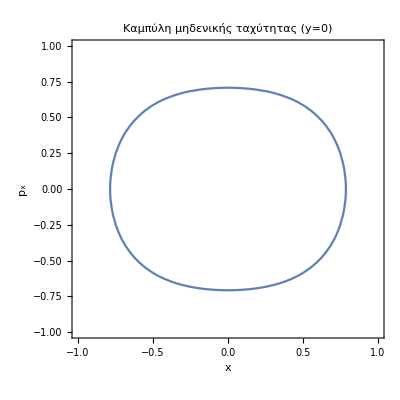

```mathematica
pySqrt[x_,px_]:=1/2(1-2 px^2-x^2-x^4)
lim1=1;
ContourPlot[pySqrt[x,px]==0,{x,-lim1,lim1},{px,-lim1,lim1},
FrameLabel->{"x","p_x"},
PlotLabel->"Καμπύλη μηδενικής ταχύτητας (y=0)"
]
```

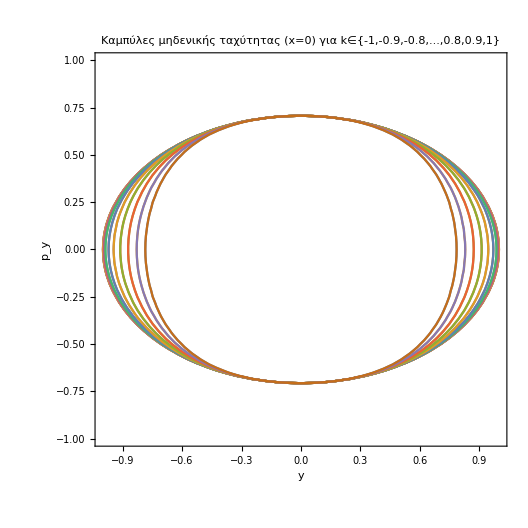

```mathematica
pxSqrt[y_,py_]:=1/2(1-2 py^2-y^2-k^4 y^4);
lim2=1;
ContourPlot[
Evaluate[Table[Evaluate[pxSqrt[y,py]/.k->i]==0,{i,-1,1,0.1}]],
{y,-lim2,lim2},{py,-lim2,lim2},
FrameLabel->{"y","p_y"},
PlotLabel->"Καμπύλες μηδενικής ταχύτητας (x=0) για k∈{-1,-0.9,-0.8,...,0.8,0.9,1}"
]
```

Βρείτε τη θέση των σημείων ισορροπίας του συστήματος, την ευστάθειά τους, και τις τιμές ενέργειας στις οποίες αντιστοιχούν.

Σημεία Ισορροπίας

```mathematica
Solve[{pxdot==0,pydot==0},{x[t],y[t]}]
```

{{x[t]→0,y[t]→0}}

Πέρα απ’ την παραπάνω (προφανή) λύση, αν αφαιρέσουμε τις δύο εξισώσεις παίρνουμε (x-k y)^3+(k(x-k y))^3=0, η οποία μας δίνει άπειρα σημεία ισορροπίας — περιλαμβανομένου και του (0,0).

```mathematica
Solve[(x[t]-k y[t])^3+k(x[t]-k y[t])^3==0,y[t]]
```

{{y[t]→x[t]/k},{y[t]→x[t]/k},{y[t]→x[t]/k}}

Ευστάθεια

Υπολογίζουμε τον πίνακα του γραμμικοποιημένου συστήματος:

```mathematica
A=Transpose@Map[D[H[x,y,px,py],Apply[Sequence,#]]&,
Outer[List,{x,y,px,py},{px,py,x,y}],
{2}]{1,1,-1,-1};
StringForm["A = ``",A//MatrixForm]
```

A = (0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1/2-3 (x-k y)^2 | -1/2+3 k (x-k y)^2 | 0 | 0
-1/2+3 k (x-k y)^2 | -1/2-3 k^2 (x-k y)^2 | 0 | 0)

Υπολογίζουμε τις ιδιοτιμές του Α στα σημεία ισορροπίας:

```mathematica
Eigenvalues[A/.{x->k y,y->y,px->0,py->0}]
```

{ⅈ,-ⅈ,0,0}

Επομένως όλα τα ΣΙ παρουσιάζουν αστάθεια.

Αντίστοιχες Ενέργειες

Η ενέργεια που αντιστοιχεί σε κάθε ΣΙ υπολογίζεται απευθείας από την Χαμιλτονιανή.

```mathematica
StringForm["Ε_(0, 0) = ``",H[0,0,0,0]]
StringForm["Ε_(k y, y) = ``",H[k y,y,0,0]]
```

Ε_(0, 0) = 0

Ε_(k y, y) = 1/4 (y+k y)^2

Σχεδιάστε την τομή Poincare για E=1/4 και E=1, αφού θέσετε

k=1.

k=1, E=1/4

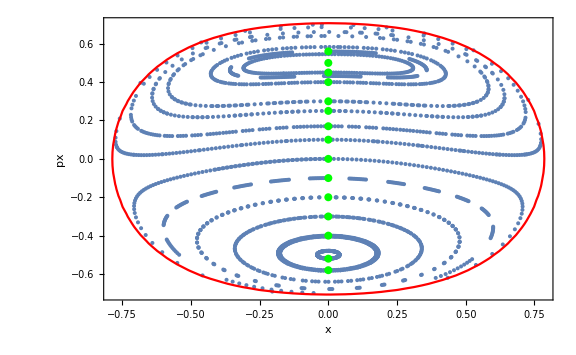

```mathematica
SectionCrossDirection=1;tmax=1000;k=1;pts={};
pySqrt[x_,px_]:=1/2(1-2 px^2-x^2-x^4);
ICxpx=Select[
{{0,0},{0,0.1},{0,0.25},{0,0.5},{0,0.56},{0,0.8},{0,-0.1},{0,-0.2},{0,-0.3},{0,-0.4},{0,-0.52},{0,-0.58},{0,-0.85},{0,0.3},{0,0.4},{0,0.17},{0,0.45}},
pySqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICxpx],i++,
IVP={deq1,deq2,deq3,deq4,x[0]==ICxpx[[i,1]],y[0]==0,px[0]==ICxpx[[i,2]],py[0]==√(SectionCrossDirection pySqrt[ICxpx[[i,1]],ICxpx[[i,2]]])};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->y[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{x[t],px[t]}]}
]
]
contour=ContourPlot[pySqrt[x,px]==0,{x,-1,1},{px,-1,1},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","px"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICxpx]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

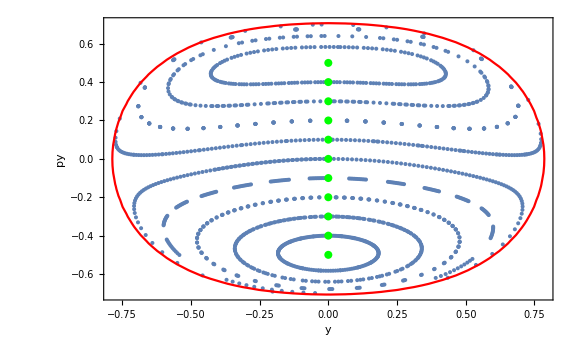

```mathematica
SectionCrossDirection=1;tmax=1000;k=1;pts={};
pxSqrt[y_,py_]:=1/2(1-2 py^2-y^2-k^4 y^4);
ICypy=Select[
{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,-0.1},{0,-0.2},{0,-0.3},{0,-0.4},{0,-0.5}},
pxSqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICypy],i++,
IVP={deq1,deq2,deq3,deq4,y[0]==ICypy[[i,1]],x[0]==0,px[0]==√(SectionCrossDirection pxSqrt[ICypy[[i,1]],ICypy[[i,2]]]),py[0]==ICypy[[i,2]]};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->x[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{y[t],py[t]}]}
]
]
contour=ContourPlot[pxSqrt[y,py]==0,{y,-1,1},{py,-1,1},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"y","py"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICypy]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

k=1, E=1

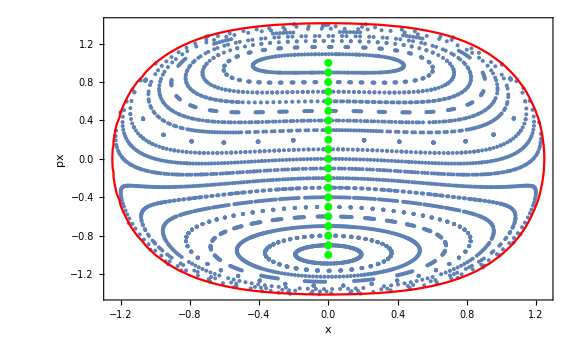

```mathematica
SectionCrossDirection=1;tmax=1000;k=1;pts={};
pySqrt[x_,px_]:=1/2(4-2 px^2-x^2-x^4);
ICxpx=Select[
{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0,0.8},{0,0.9},{0,1},{0,-0.1},{0,-0.2},{0,-0.3},{0,-0.4},{0,-0.5},{0,-0.6},{0,-0.7},{0,-0.8},{0,-0.9},{0,-1}},
pySqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICxpx],i++,
IVP={deq1,deq2,deq3,deq4,x[0]==ICxpx[[i,1]],y[0]==0,px[0]==ICxpx[[i,2]],py[0]==√(SectionCrossDirection pySqrt[ICxpx[[i,1]],ICxpx[[i,2]]])};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->y[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{x[t],px[t]}]}
]
]
contour=ContourPlot[pySqrt[x,px]==0,{x,-2,2},{px,-2,2},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","px"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICxpx]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

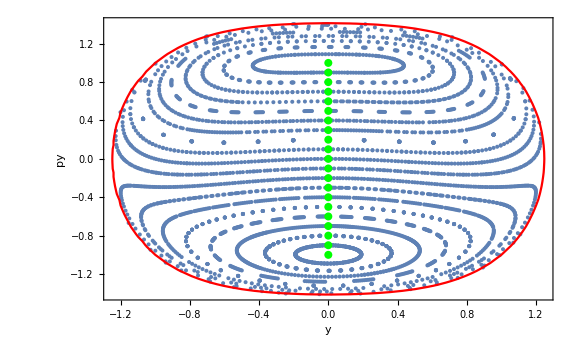

```mathematica
SectionCrossDirection=1;tmax=1000;k=1;pts={};
pxSqrt[y_,py_]:=1/2(4-2 py^2-y^2-k^4 y^4);
ICypy=Select[
{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0,0.8},{0,0.9},{0,1},{0,-0.1},{0,-0.2},{0,-0.3},{0,-0.4},{0,-0.5},{0,-0.6},{0,-0.7},{0,-0.8},{0,-0.9},{0,-1}},
pxSqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICypy],i++,
IVP={deq1,deq2,deq3,deq4,y[0]==ICypy[[i,1]],x[0]==0,px[0]==√(SectionCrossDirection pxSqrt[ICypy[[i,1]],ICypy[[i,2]]]),py[0]==ICypy[[i,2]]};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->x[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{y[t],py[t]}]}
]
]
contour=ContourPlot[pxSqrt[y,py]==0,{y,-2,2},{py,-2,2},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"y","py"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICypy]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

k=2.

k=2, E=1/4

{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0.1,0.65},{0,-0.1},{0,-0.2},{0,-0.25}}

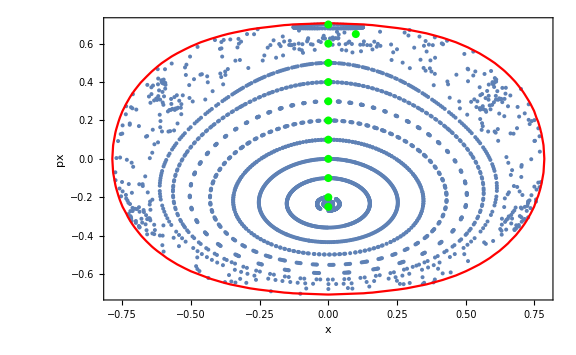

```mathematica
SectionCrossDirection=1;tmax=1000;k=2;pts={};
pySqrt[x_,px_]:=1/2(1-2 px^2-x^2-x^4);
ICxpx=Select[
{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0.1,0.65},{0,0.8},{0,0.9},{0,0.99},{0.44,0.7},{0,0.85},{0.12,0.85},{0,-0.1},{0,-0.2},{0,-0.25}},
pySqrt[#[[1]],#[[2]]]>0&]
For[i=1,i≤Length[ICxpx],i++,
IVP={deq1,deq2,deq3,deq4,x[0]==ICxpx[[i,1]],y[0]==0,px[0]==ICxpx[[i,2]],py[0]==√(SectionCrossDirection pySqrt[ICxpx[[i,1]],ICxpx[[i,2]]])};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->y[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{x[t],px[t]}]}
]
]
contour=ContourPlot[pySqrt[x,px]==0,{x,-2,2},{px,-2,2},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","px"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICxpx]},
ImageSize->Large
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

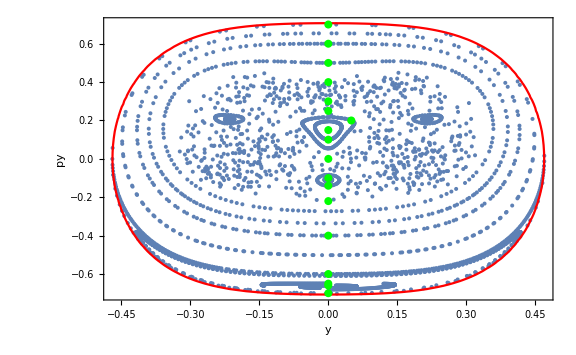

```mathematica
SectionCrossDirection=1;tmax=1000;k=2;pts={};
pxSqrt[y_,py_]:=1/2(1-2 py^2-y^2-k^4 y^4);
ICypy=Select[
{{0,0},{0,0.1},{0,0.15},{0,0.25},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0.05,0.2},{0,-0.1},{0,-0.14},{0,-0.22},{0,-0.4},{0,-0.6},{0,-0.65},{0,-0.66},{0,-0.7}},
pxSqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICypy],i++,
IVP={deq1,deq2,deq3,deq4,y[0]==ICypy[[i,1]],x[0]==0,px[0]==√(SectionCrossDirection pxSqrt[ICypy[[i,1]],ICypy[[i,2]]]),py[0]==ICypy[[i,2]]};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->x[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{y[t],py[t]}]}
]
]
contour=ContourPlot[pxSqrt[y,py]==0,{y,-1,1},{py,-1,1},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"y","py"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICypy]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

k=2, E=1

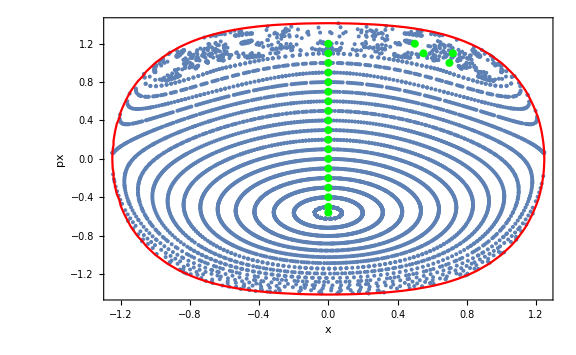

```mathematica
SectionCrossDirection=1;tmax=1000;k=2;pts={};
pySqrt[x_,px_]:=1/2(4-2 px^2-x^2-x^4);
ICxpx=Select[
{{0,0},{0,0.1},{0,0.2},{0,0.3},{0,0.4},{0,0.5},{0,0.6},{0,0.7},{0,0.8},{0,0.9},{0,1},{0,1.1},{0,1.2},{0.55,1.1},{0.7,1},{0.72,1.1},{0.5,1.2},{0,-0.1},{0,-0.2},{0,-0.3},{0,-0.4},{0,-0.5},{0,-0.56}},
pySqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICxpx],i++,
IVP={deq1,deq2,deq3,deq4,x[0]==ICxpx[[i,1]],y[0]==0,px[0]==ICxpx[[i,2]],py[0]==√(SectionCrossDirection pySqrt[ICxpx[[i,1]],ICxpx[[i,2]]])};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->y[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{x[t],px[t]}]}
]
]
contour=ContourPlot[pySqrt[x,px]==0,{x,-2,2},{px,-2,2},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","px"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICxpx]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

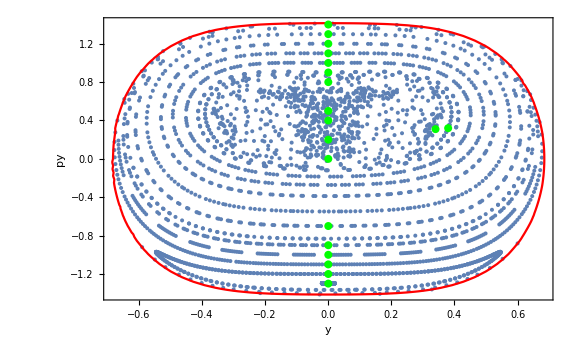

```mathematica
SectionCrossDirection=1;tmax=1000;k=2;pts={};
pxSqrt[y_,py_]:=1/2(4-2 py^2-y^2-k^4 y^4);
ICypy=Select[
{{0,0},{0,0.2},{0,0.4},{0,0.5},{0,0.8},{0,0.9},{0,1},{0,1.1},{0.34,0.31},{0.38,0.32},{0,1.2},{0,1.3},{0,1.4},{0,-0.7},{0,-0.9},{0,-1},{0,-1.1},{0,-1.2},{0,-1.3}},
pxSqrt[#[[1]],#[[2]]]>0&];
For[i=1,i≤Length[ICypy],i++,
IVP={deq1,deq2,deq3,deq4,y[0]==ICypy[[i,1]],x[0]==0,px[0]==√(SectionCrossDirection pxSqrt[ICypy[[i,1]],ICypy[[i,2]]]),py[0]==ICypy[[i,2]]};
NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->x[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{y[t],py[t]}]}
]
]
contour=ContourPlot[pxSqrt[y,py]==0,{y,-2,2},{py,-2,2},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"y","py"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICypy]}
];
Show[poincarePlot,contour,PlotRange->All,ImageSize->Large]
```

Για k=1/2 και E=1/4 εντοπίστε και σχεδιάστε στο επίπεδο xy μερικές ενδεικτικές περιοδικές τροχιές.

Βρείτε ένα ολοκλήρωμα (πολυώνυμο 2^ου βαθμού ως προς την ταχύτητα) για k=-1.

Έστω F=a px^2+b py^2+c px+d py+e το ολοκλήρωμα που ζητάμε. Θα πρέπει να είναι [H,I]=0.

```mathematica
k=1;
F[x_,y_,px_,py_]:=a px^2+b py^2+c px+d py/.{c->1,d->0};
D[H[x,y,px,py],x]D[F[x,y,px,py],px]-D[F[x,y,px,py],x]D[H,px]+D[H[x,y,px,py],y]D[F[x,y,px,py],py]-D[H[x,y,px,py],py]D[F[x,y,px,py],y]==0
Solve[%,b]//FullSimplify
```

2 b py H^(0,1,0,0)[x,y,px,py]+(1+2 a px) H^(1,0,0,0)[x,y,px,py]==0

{{b→-((1+2 a px) H^(1,0,0,0)[x,y,px,py])/(2 py H^(0,1,0,0)[x,y,px,py])}}

Άσκηση 5.2

Για το Γαλαξιακό δυναμικό Henon-Heiles

V=a/2(x^2+y^2)-x^2 y+ε/3 y^3

και για τιμές των παραμέτρων a=1, ε=1.5, E_0=0.05, να γίνουν τα ακόλουθα:

```mathematica
ClearAll["Global`*"]
H[x_,y_,px_,py_]:=1/2(px^2+py^2)+1/2(x^2+y^2)-x^2 y+1/2 y^3
V[x_,y_]:=1/2(x^2+y^2)-x^2 y+1/2 y^3;
xdot=D[H[x,y,px,py],px]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq1=x'[t]==xdot;
ydot=D[H[x,y,px,py],py]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq2=y'[t]==ydot;
pxdot=-D[H[x,y,px,py],x]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq3=px'[t]==pxdot;
pydot=-D[H[x,y,px,py],y]/.{x->x[t],y->y[t],px->px[t],py->py[t]};
deq4=py'[t]==pydot;
Column[{
StringForm["ẋ = ``",xdot],
StringForm["ẏ = ``",ydot],
StringForm["OverDot[px] = ``",pxdot],
StringForm["OverDot[py] = ``",pydot]
},Alignment->Center]
```

ẋ = px[t]
ẏ = py[t]
OverDot[px] = -x[t]+2 x[t] y[t]
OverDot[py] = x[t]^2-y[t]-(3 y[t]^2)/2

Βρείτε τα σημεία ισορροπίας.

```mathematica
si=Solve[{pxdot==0,pydot==0},{x[t],y[t]}];
A=Transpose@Map[D[H[x,y,px,py],Apply[Sequence,#]]&,
Outer[List,{x,y,px,py},{px,py,x,y}],
{2}]{1,1,-1,-1};
Column[{
StringForm["Σημεία Ισορροπίας: ``",TableForm[si,TableAlignments->Center]],
StringForm["A = ``",A//MatrixForm],
StringForm["(0,-3/2) → `` ⟹ αστάθεια",Eigenvalues[A]/.{x->0,y->3/2}],
StringForm["(0,0) → `` ⟹ ευστάθεια (κεντρικό σημείο)",Eigenvalues[A]/.{x->0,y->0}],
StringForm["(-1/2√(7/2),1/2) → `` ⟹ αστάθεια",Eigenvalues[A]/.{x->-1/2 √(7/2),y->1/2}],
StringForm["(1/2√(7/2),1/2) → `` ⟹ αστάθεια",Eigenvalues[A]/.{x->1/2 √(7/2),y->1/2}]
},Alignment->Center]
si=Map[Last,si,{2}];
```

Σημεία Ισορροπίας: x[t]→0 | y[t]→-2/3
x[t]→0 | y[t]→0
x[t]→-(√(7/2))/2 | y[t]→1/2
x[t]→(√(7/2))/2 | y[t]→1/2
A = (0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1+2 y | 2 x | 0 | 0
2 x | -1-3 y | 0 | 0)
(0,-3/2) → {-ⅈ √(11/2),ⅈ √(11/2),-√2,√2} ⟹ αστάθεια
(0,0) → {-ⅈ,ⅈ,-ⅈ,ⅈ} ⟹ ευστάθεια (κεντρικό σημείο)
(-1/2√(7/2),1/2) → {-ⅈ √(7/2),ⅈ √(7/2),-1,1} ⟹ αστάθεια
(1/2√(7/2),1/2) → {-ⅈ √(7/2),ⅈ √(7/2),-1,1} ⟹ αστάθεια

Υπολογίστε για ποιες τιμές ενέργειας έχουμε περατωμένες κινήσεις γύρω από το (0,0).

-Graphics3D-

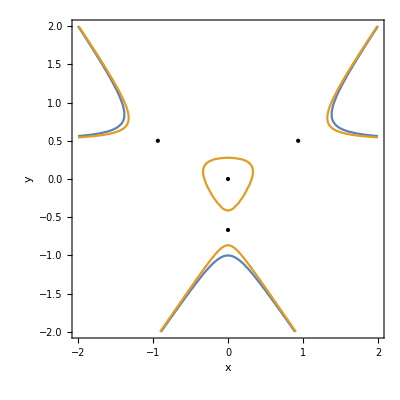

```mathematica
Plot3D[{V[x,y],0,0.05},{x,-2,2},{y,-2,2},Mesh->None,ImageSize->Medium,PlotRange->{-0.1,0.5},AxesLabel->{"x","y","V"}]
ContourPlot[{V[x,y]==0,V[x,y]==0.05},{x,-2,2},{y,-2,2},FrameLabel->{"x","y"},GridLines->{Table[i,{i,-2,2,0.2}],Table[i,{i,-2,2,0.2}]},
Epilog->{Point[si]}]
```

Για τις περατωμένες τροχιές, σχεδιάστε την τομή Poincare του συστήματος που ορίζεται από την {(x,ẋ),p_y<0}.

{{0.919512,0.369286},{-0.02942,0.890944},{-0.477151,-0.945915},{0.663963,0.370748},{-0.258512,0.826447},{0.530801,0.223712},{0.564936,0.949771},{-0.05031,-0.611371},{0.133578,0.533242},{0.627155,0.436239},{0.914183,0.113293},{0.95223,-0.449838},{-0.20723,0.961738},{0.492542,-0.101183},{0.123736,0.460231},{0.934934,0.0874919},{0.288722,-0.392125},{0.0247611,-0.847216},{-0.552012,-0.0776361},{-0.0141851,-0.83181},{-0.500962,0.815614},{0.451097,0.273682},{0.523526,0.834798},{-0.994805,-0.745268},{-0.726784,-0.0867314},{-0.207607,-0.521208},{-0.0772323,0.900713},{-0.33775,0.71294},{-0.907514,0.741485},{-0.543199,-0.62529},{-0.748489,0.16555},{0.641565,-0.685273},{-0.457819,-0.477576},{-0.418168,-0.33328},{-0.211668,0.692569},{-0.752624,0.747967},{-0.352075,0.546719},{0.516151,0.306045},{0.710308,0.508619},{-0.535724,-0.998531}}

NDSolve::ndsz: At t == 3.64216, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.96261, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.29892, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

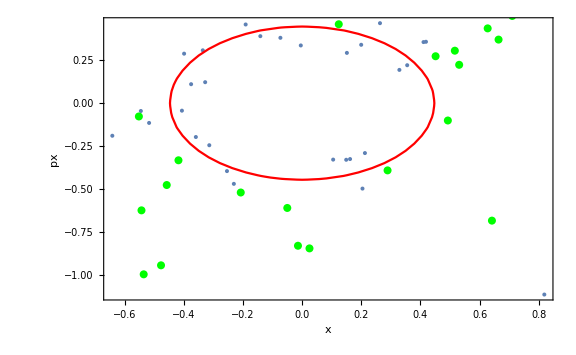

```mathematica
SectionCrossDirection=1;tmax=1000;k=1;pts={};
pySqrt[x_,px_]:=-2(1/10-1/2 px^2-1/2 x^2)
ICxpx=Select[
Table[RandomReal[{-1,1}],{50},{2}],
pySqrt[#[[1]],#[[2]]]>0&]
For[i=1,i≤Length[ICxpx],i++,
IVP={deq1,deq2,deq3,deq4,x[0]==ICxpx[[i,1]],y[0]==0,px[0]==ICxpx[[i,2]],py[0]==√(SectionCrossDirection pySqrt[ICxpx[[i,1]],ICxpx[[i,2]]])};
sol=NDSolve[IVP,{x[t],y[t],px[t],py[t]},{t,0,tmax},
Method->{EventLocator,"Event"->y[t],"Direction"->SectionCrossDirection,"EventAction":>AppendTo[pts,{x[t],px[t]}]}
]
]
contour=ContourPlot[pySqrt[x,px]==0,{x,-1,1},{px,-1,1},
ContourStyle->Red
];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","px"},
PlotStyle->{PointSize[0.005]},
Epilog->{Green,PointSize[0.01],Point[ICxpx]},
PlotRange->All
];
Show[{poincarePlot,contour},PlotRange->All,ImageSize->Large]
```

Για μερικές αρχικές συνθήκες της δικής σας επιλογής σχεδιάστε τις αντίστοιχες τροχιές στο επίπεδο xy και στον χώρο xyp_x ή xyp_y και χαρακτηρίστε τις (περιοδικές, ημιπεριοδικές, χαοτικές).

NDSolve::ndsz: At t == 38.8792, step size is effectively zero; singularity or stiff system suspected.

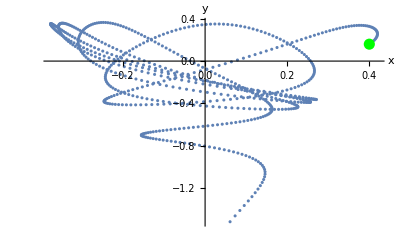

-Graphics3D-

```mathematica
IC={{0.99,0.81,-0.42,-0.9},{0.37,-0.92,-0.84,-0.15},{0.4,0.16,0.1,0.25},{-0.11,0.48,0.05,-0.28},{-0.29,0.25,-0.07,0.71}};
i=3;
IVP={deq1,deq2,deq3,deq4,x[0]==IC[[i,1]],y[0]==IC[[i,2]],px[0]==IC[[i,3]],py[0]==IC[[i,4]]};
sol=NDSolve[IVP,{x,y,px,py},{t,0,5000}];
xt=x/.sol[[1]];
yt=y/.sol[[1]];
pxt=px/.sol[[1]];
pts=Table[{xt[t],yt[t],pxt[t]},{t,0,38.8,0.05}];
ListPlot[pts[[All,1;;2]],AxesLabel->{"x","y"},Epilog->{Green,PointSize[0.02],Point[IC[[i,1;;2]]]}]
Graphics3D[Line[pts],Axes->True,AxesLabel->{"x","y","px"}]
```